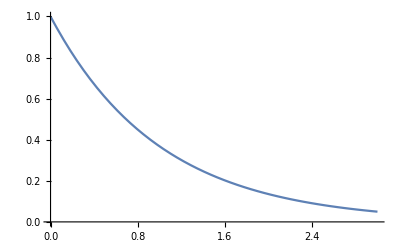

```mathematica
Plot[Exp[-x],{x,0,3}]
```

```mathematica
D[Exp[-x],x]
```

-ⅇ^-x

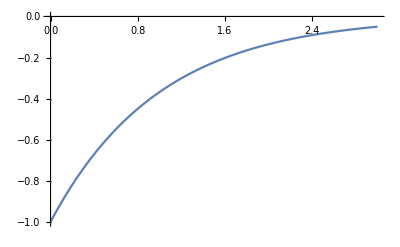

```mathematica
Plot[-ⅇ^-x,{x,0,3}]
```

```mathematica
L = t1(t-t1)/(t1(1-q)^2+(t-t1)q^2)
```

((t-t1) t1)/(q^2 (t-t1)+(1-q)^2 t1)

```mathematica
((t-t1) t1)/(q^2 (t-t1)+(1-q)^2 t1)
```

((t-t1) t1)/(q^2 (t-t1)+(1-q)^2 t1)

```mathematica
D[L,t1]
```

-(((1-q)^2-q^2) (t-t1) t1)/((q^2 (t-t1)+(1-q)^2 t1)^2)+(t-t1)/(q^2 (t-t1)+(1-q)^2 t1)-t1/(q^2 (t-t1)+(1-q)^2 t1)

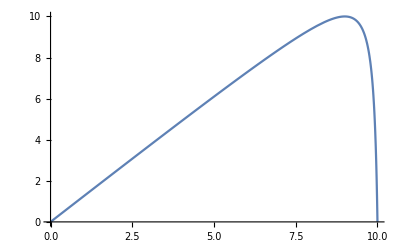

```mathematica
Plot[L /. {t-> 10, q -> 0.9},{t1,0,10}]
```

```mathematica
Maximize[L,t1]
```

{Piecewise[{{t, t>0&&q==1/2}, {-∞, !((t>0&&q==1/2)||(t==0&&q>1/2)||(t==0&&q<1/2)||(t>0&&q>1/2)||(t>0&&q<1/2)||t<0)}, {∞, True}}],{t1→Piecewise[{{Indeterminate, !(t>0&&q==1/2)}, {t/2, True}}]}}

```mathematica
Solve[D[L,t1]==0,t1]
```

```mathematica
{{t1->q t},{t1->(q t)/(-1+2 q)}} /. {q -> .5,t->10}
```

{{t1→6.},{t1→30.}}

```mathematica
ClearAll["Global`*"]
```

```mathematica
L2 = Exp[-A(t1+q*g)]+Exp[-A((t-t1)+(1-q)g)]
```

ⅇ^(-A (g (1-q)+t-t1))+ⅇ^(-A (g q+t1))

```mathematica
Solve[D[L2,t1] == 0,t1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t1→1/2 (g-2 g q+t)}}